# Rosseler System: Poincare Sections etc.

We want to store up all the Rosseler points were we cross a vertical plane or hit the top of the ski jump.  Then we want to think about and see what those points look like!

## Lorentz Ski Jump Points.

```mathematica
{a,b,c}={0.2,0.2,5.7};
f[{x_,y_,z_}]:= {-y-z,x + a*y, b +z*(x-c)}
TMax=250;
StuffPlace={};
Quiet[
sol = NDSolveValue[{p'[t]==f[p[t]],p[0]=={0.2,0.4,13.4}},p,{t,0, TMax},
Method->{"EventLocator",
"Event"->(p'[t])⟦3⟧,
"EventAction":>(StuffPlace={StuffPlace,p[t]}),
"Direction"->-1}];
]
Pic=ParametricPlot3D[sol[t],{t,0,TMax},
PlotPoints->200,
PlotRange->All,
PlotStyle->Thin];
StuffPlace=Partition[Flatten[StuffPlace],3];
Show[Pic, 
ListPointPlot3D[ StuffPlace,PlotStyle->Directive[Red,PointSize[0.02]]]]
```

-Graphics3D-

## Poincare Section Points.

These are points where the solution crosses a plane from either +→-  are -→+.   We chose vertical plane through the lower equilibrium point.  We looked at two planes one containing the line y=x+b and the other containing y=-x+b.  Here is the one containing y=x+b with normal {1,-1,0}.

```mathematica
{a,b,c}={0.2,0.2,5.7};
center = {0.007026204834100129,-0.035131024170500645,0.035131024170500645};
{n1,n2}={{1,1,0},{1,-1,0}}; 
PlanePic= ContourPlot3D[ ({x,y,z}- center).n2 ==0, {x, -12,12},{y,-12,12},{z, 0, 20},
ContourStyle->Opacity[0.5]];
f[{x_,y_,z_}]:= {-y-z,x + a*y, b +z*(x-c)}
TMax=250;
StuffPlace={};
Quiet[
sol = NDSolveValue[{p'[t]==f[p[t]],p[0]=={0.2,0.4,13.4}},p,{t,0, TMax},
Method->{"EventLocator",
"Event":>((p[t]-center). n2),
"EventAction":>(StuffPlace={StuffPlace,p[t]}),
"Direction"->-1}];
]
Pic=ParametricPlot3D[sol[t],{t,0,TMax},
PlotPoints->200,
PlotRange->All,
PlotStyle->Thin];
StuffPlace=Partition[Flatten[StuffPlace],3];
m=Length[StuffPlace];
Show[Pic, 
PlanePic,
Graphics3D[Table[ {PointSize[0.02],Hue[i/(m+1)],Point[StuffPlace⟦i⟧]},{i, m}]],
AxesLabel->{"x","y","z"},
FaceGrids->All]
```

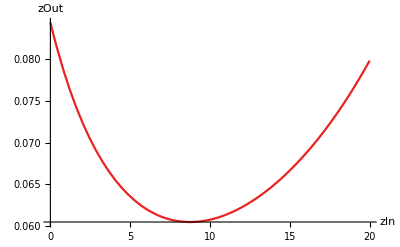

```mathematica
ForwardMap[p0_List]:=Catch[
NDSolveValue[{p'[t]==f[p[t]],p[0]==p0},p,{t,0, 10^3},
Method->{"EventLocator",
"Event":>((p[t]-center). n2),
"EventAction":>Throw[end=p[t],"StopIntegration"],
"Direction"->-1}]; end]

xp=1.5; 
Plot[ ForwardMap[{xp,xp-0.042157229004600776,z}]⟦3⟧,{z,0,20},
PlotRange->All,
AxesLabel->{"zIn","zOut"},
ColorFunction->Function[{z,zOut},Hue[zOut]]
]
```

```mathematica
Pic=ParametricPlot3D[ ForwardMap[{x,x-0.042157229004600776,z}],
{x, 0.5,5},
{z,0,20},
PlotRange->All,
AxesLabel->{"xOut","yOut","zOut"}
]
```

-Graphics3D-

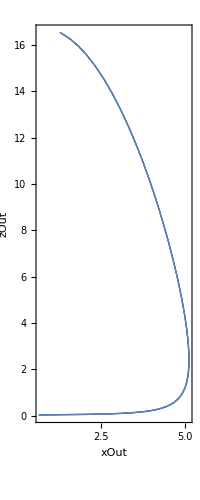

```mathematica
Pic=ParametricPlot[ Hmm= ForwardMap[{x,x-0.042157229004600776,z}];
Hmm⟦{1,3}⟧,
{x, 0.5,5},
{z,0,20},
PlotRange->All,
AxesLabel->{"xOut","zOut"}
]
```

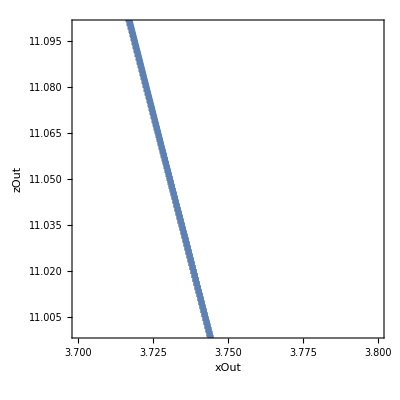

```mathematica
Show[Pic,
PlotRange->{{3.7,3.8},{11,11.1}}]
```

```mathematica
ParametricPlot3D[ r{2Cos[θ], Sin[θ],0},{θ,0, 2π},{r, 0.2,1},
ColorFunction->Function[{x,y,r,θ},Hue[r/2]],
PlotPoints->50]
```

-Graphics3D-

```mathematica
ForwardMap[{0.1,0.2,0.3}]
```

NDSolveValue::bdmtd: The value of the option Method -> {EventLocator,Event:>(p[t]-center).n2,Null,Direction→-1} is not a known built-in method, a symbol that could be a user-defined method, or a list with a name followed by method options.

NDSolveValue[{p'[t]==f[p[t]],p[0]=={0.1,0.2,0.3}},p,{t,0,250},Method→{EventLocator,Event:>(p[t]-center).n2,Null,Direction→-1}]